Elliptic Curves Group Law:

One a vaguely think of an elliptic curve as the set of solution of a cubic equation, satisfying some extra conditions which will be looked at later. With some change of coordinates, we can usually transform the cubic to the form: y^2 = x^3 + Ax + B. It is easier to describe the elliptic curve geometrically. For example, an elliptic curve make look like:

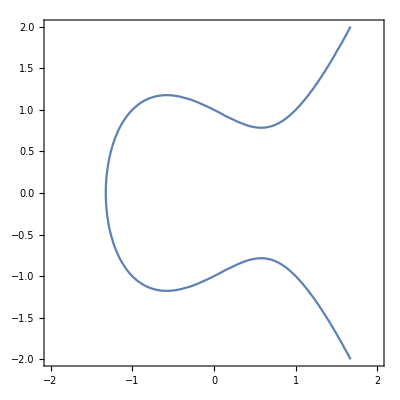

```mathematica
ContourPlot[y^2 == x^3 -x + 1, {x, -2, 2}, {y, -2, 2}, Axes->True]
```

What makes an elliptic curve interesting is that given two points P, Q we can create another point on the elliptic curve. Intuitively, we may try to do this by constructing a line from P to Q, then finding the third point of intersection denoted as S.

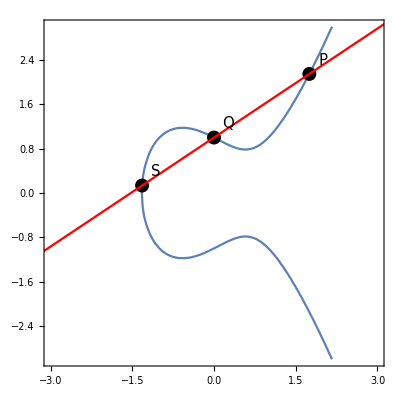

```mathematica
P = {1.75,Sqrt[(1.75)^3 - (1.75)+1]};
Q = {0,1};
m1= (Q[[2]] - P[[2]])/(Q[[1]] - P[[1]]);
b1 = P[[2]] - m1*P[[1]];
x3 = m1^2 - P[[1]] - Q[[1]];
y3 = m1*x3 + b1;
S={x3,y3};
Show[
(* Plots *)
ContourPlot[y^2 == x^3 -x +1, {x, -3, 3}, {y, -3, 3},Axes->True],
ListPlot[{P,Q,S},PlotStyle -> {AbsolutePointSize[10],Black}],
Plot[m1*x + b1, {x, -4, 4},PlotStyle->{Red}],
Graphics[{
(* Labels for points *)
Inset[Style[StringForm["P"], 15], P + {.25, .25}],
Inset[Style[StringForm["Q"], 15], Q + {.25, .25}],
Inset[Style[StringForm["S"], 15], S + {.25, .25}]
}]
]
```

While this is useful, it fails to satisfy the axioms of a group, namely there is no identity point.
To fix this, we’ll introduce some fixed point O. This will become part of our definition of an elliptic curve: an elliptic curve is the curve + the fixed point O. Then, we will construct a line from S to O and find the third point of intersection denoted as R.

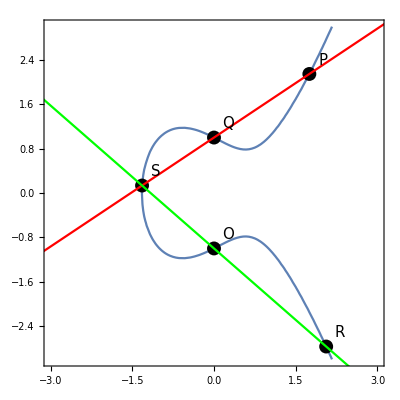

```mathematica
o = {0,-Sqrt[(0)^3 - (0)+1]};
m2 = (S[[2]] - o[[2]])/(S[[1]] - o[[1]]);
b2 = S[[2]] - m2*S[[1]];
x3 = m2^2 - S[[1]] - o[[1]];
y3 = m2*x3 + b2;
R={x3,y3};
Show[
(* Plots *)
ContourPlot[y^2 == x^3 -x +1, {x, -3, 3}, {y, -3, 3},Axes->True],
ListPlot[{P,Q,S,o,R},PlotStyle -> {AbsolutePointSize[10],Black}],
Plot[m1*x + b1, {x, -4, 4},PlotStyle->{Red}],
Plot[m2*x + b2, {x, -4, 4},PlotStyle->{Green}],
Graphics[{
(* Labels for points *)
Inset[Style[StringForm["P"], 15], P + {.25, .25}],
Inset[Style[StringForm["Q"], 15], Q + {.25, .25}],
Inset[Style[StringForm["S"], 15], S + {.25, .25}],
Inset[Style[StringForm["O"], 15], o + {.25, .25}],
Inset[Style[StringForm["R"], 15], R + {.25, .25}]
}]
]
```

We will define the group law to be P + Q = R. With this definition, it’s not too hard to see that this is a group law. However, there were some assumption that we made.

## Assumptions:

We assume that: the curve is nonsingular and we have to work over the Complex Projective Plane. We need the tangent line at every point to be well defined (unique), thus we require to be nonsingular at every point. In order to make the group law work, we need Bezout' s Theorem, which implies that we must work over Complex Projective Plane. So, we usually tale O to be the point at infinity. The Theorem tells us that a line and a curve intersects the curve at 3 points. So, when we have two points, we can always find the third point of intersection.

### Bezout’s Theorem:

```mathematica
Entity["MathWorld","BezoutsTheorem"]["LongTypesetDescription"]
```

Bézout’s theorem for curves states that, in general, two algebraic curves of degrees m and n intersect in m·n points and cannot meet in more than m·n points unless they have a component in common (i.e., the equations defining them have a common factor; Coolidge 1959, p. 10).
Bézout’s theorem for polynomials states that if P and Q are two polynomials with no roots in common, then there exist two other polynomials A and B such that AP+BQ==1. Similarly, given N polynomial equations of degrees n_1, n_2, …n_N in N variables, there are in general n_1 n_2⋯n_N common solutions.
Séroul uses the term Bézout’s theorem for the following two theorems. 
1. Let a,b∈ℤ be any two integers, then there exist u,v∈ℤ such that
au+bv==GCD(a,b).
2. Two integers a and b are relatively prime if there exist u,v∈ℤ such that
au+bv==1.

### Complex Projective Plane:

```mathematica
Entity["MathWorld","ComplexProjectivePlane"]["TypesetDescription"]
```

The set ℙ^2 is the set of all equivalence classes [a,b,c] of ordered triples (a,b,c)∈ℂ^3\(0,0,0) under the equivalence relation (a,b,c)∼(a',b',c') if (a,b,c)==(λ a',λ b',λ c') for some nonzero complex number λ.

### Nonsingular:

```mathematica
Entity["MathWorld","SingularPoint"]["TypesetDescription"]
```

A singular point of an algebraic curve is a point where the curve has “nasty” behavior such as a cusp or a point of self-intersection (when the underlying field K is taken as the reals). More formally, a point (a,b) on a curve f(x,y)==0 is singular if the x and y partial derivatives of f are both zero at the point (a,b). (If the field K is not the reals or complex numbers, then the partial derivative is computed formally using the usual rules of calculus.)
The following table gives some representative named curves that have various types of singular points at their origin.

## Group Law:

Below is an interactive model of an elliptic curve. You can move the points P and Q, and it will calculate P + Q = R. Also, you can adjust the parameters A and B for the cubic equation.
Note: there are cases in which it will fail for values of A and B. Quit the Kernel and rerun.

```mathematica
Manipulate[
 (* Ensuring P is on the elliptic curve *)
 If[P[[1]]^3 + A*P[[1]] + B != P[[2]]^2,
  If[P[[2]] > 0, P[[2]] = Sqrt[P[[1]]^3 + A*P[[1]] + B],
   P[[2]] = -Sqrt[P[[1]]^3 + A*P[[1]] + B]
   ]
  ];
 (* Ensuring Q is on the elliptic curve *)
 If[Q[[1]]^3 + A*P[[1]] + B != Q[[2]]^2,
  If[Q[[2]] > 0, Q[[2]] = Sqrt[Q[[1]]^3 + A*Q[[1]] + B],
   Q[[2]] = -Sqrt[Q[[1]]^3 + A*Q[[1]] + B]
   ]
  ];
 (* Calculating R = (x3,-y3) *)
 m = (Q[[2]] - P[[2]])/(Q[[1]] - P[[1]]);
 b = P[[2]] - m*P[[1]];
 x3 = m^2 - P[[1]] - Q[[1]];
 y3 = m*x3 + b;
 Show[
  (* Equation for Elliptic Curve *)
  ContourPlot[y^2 == x^3 + A*x + B, {x, -4, 4}, {y, -4, 4},Axes->True],
(* Plots *)
  Plot[m*x + b, {x, -4, 4},PlotStyle->Red],
  ListPlot[{{x3, y3}, {x3, -y3}}, PlotStyle -> {AbsolutePointSize[10], Black}],
  Graphics[{
(* Labels *)
    Green,Line[{{x3, -4}, {x3, 4}}],
Black, Inset[Style[StringForm["P"], 15], P + {.25, .25}],
Inset[Style[StringForm["P = ``",P], 15], {-2.75, 4}],
    Inset[Style[StringForm["Q"], 15], Q + {.25, .25}],
Inset[Style[StringForm["Q = ``",Q], 15], {-2.75, 3.75}],
    Inset[Style[StringForm["R", {x3, -y3}], 15], {x3, -y3} + {0, .25}],
Inset[Style[StringForm["R = ``",{x3,-y3}], 15], {-2.75, 3.5}],
Inset[Style[StringForm["S"], 15], {x3,y3} + {0,.25}],
    Inset[Style[StringForm["O"], 15], {x3, 4}]
    }],ImageSize->Large
  ],
 {{A, -1}, -10, 10}, {{B, 1}, -10, 10}, {{P, {1, 1}}, Locator}, {{Q, {0, 1}}, Locator}
 ]
```

## Identity:

The identity element is the fixed point O. Let P ∈ E, then P + O = P = O + P
O is usually taken to be the point at infinity, and we will assume this to be the case for future calculations. To given some intuition on this point at infinity, the line OverBar[OP] is a vertical line for any point P.

## Closure:

Let P, Q ∈ E, then P + Q = R ∈ E.
The point R is the result of constructing two lines and finding intersections between the two curves, so R will be on the elliptic curve. 
Algebraically:
Let P = (x1, y1), Q = (x2, y2),  R = (x3, y3)
λ = (y2-y1)/(x2-x1)
ν = y2 - λ*x2 = y1 - λ*x1
x3 = λ^2 - x1 - x2
y3 = -(λ*x3 + ν)

## Inverse:

Let P ∈ E, then there exists -P such that P + (-P) = O = (-P) + P
The inverse -P can be found by finding the intersection between the line OverBar[OP] and the elliptic curve.
Algebraically:
Let P = (x, y), then -P = (x, -y).

## Associativity:

Let P, Q, R ∈ E, then (P + Q) + R = P + (Q + R).
Difficult to show, believe me that it’s true.

## Commutativity:

Let P, Q ∈ E, then P + Q = Q + P.
It turns out that (E,+) is also an Abelian Group. Constructing the line OverBar[PQ] is the same as constructing the line OverBar[QP].

# Rational Points on the Elliptic Curve

The thing we want to study on top of elliptic curves are the rational points on an elliptic curve. We’re interested in the points P = (x,y) where x, y ∈ ℚ. 
The first equation we should ask is: does there even exist a rational point on the elliptic curve? Unfortunately, in general the answer is we don’t know. Thus, we will assume there exists at least one rational point, which we usually take to be the fixed point O. This is why it is part of definition of an elliptic curve.
So assuming we have one rational point on the elliptic curve, the question now becomes: can we find another one or describe the rest of them? Alternatively, given rational points P, Q, can we find another one? Yes, we can use the group law defined above. It’s not too hard to see that if both P, Q are rational, then P + Q = R will also be rational. 
Thus the rational points on the elliptic curve E(ℚ) form a an abelian group under addition: (E(ℚ), +).
Our goal is to study this group, and this is what Mordell-Weil Theorem is all about:

```mathematica
Entity["MathWorld","Mordell-WeilTheorem"]["TypesetDescription"]
```

For elliptic curves over the rationals ℚ, the group of rational points is always finitely generated (i.e., there always exists a finite set of group generators). This theorem was proved by Mordell (1922–23) and extended by Weil to Abelian varieties over number fields.

The proof of this is long and hard, so instead I will give a sketch of the main steps of the proof. It is done in two main steps: the theory of heights and the Weak Mordell-Weil Theorem.

### Theory of Heights:

Let x = m/n in lowest terms. The height is defined as H(x) = max { |m|, |n| }
To make calculations easier, we will look at the log of the height: h(x) = log H(x). Also, we want to look at the heights of points P = (x,y) ∈ E(ℚ), so we will define h(P) = h(x).
This leads into the first of three lemmas we will look at:

#### Lemma 1:

∀ C ∈ ℝ, the set { P ∈ E(ℚ) | h(P) ≤ C } is finite

Since h(P) = h(x), if h(x) ≤ C, then |m|, |n| ≤ C. There are finite such x ϵ  ℚ for which this is possible. Then looking at the equation, for some x, we see that there are 2 solution for y. In all, this gives us a finite such points for which this is possible

#### Lemma 2 :

Let P_0 ∈ E(ℚ) be a fixed point, then constant ∃k_0 = k_0(P_0,E) so that 
∀ P ∈ E(ℚ) 	h(P + P_0) ≤ 2h(P) + k_0

#### Lemma 3:

∃ k = k(E) so that 
∀ P ∈ E(ℚ) 	h(2P) ≥ 4h(P) - k

Lemma 2 and Lemma 3 are not too difficult to prove, they only require some algebra calculations.

### Weak Mordell-Weil Theorem:

The index E(ℚ) / 2E(ℚ) is finite.

This is much harder to prove, and in this general form, it requires more advanced methods. However, if we add an extra hypothesis that there exists a rational 2 torsion point.
∃ P ∈ E(ℚ)[2], meaning 2P = P + P = O.
Then, will still difficult, it can be done with elementary tools. I will just mention that one such way is to look at the representation of elliptic curves over ℂ / ⋀ (lattice).

### Descent Theorem:

Everything is tied together through the Descent Theorem, which simply states:

3 height lemmas + Weak Mordell-Weil Theorem ⇒ Model-Weil Theorem

Thus, we know that the rational points on the elliptic curve are a finitely generated abelian group.